# SDL Complexity

```mathematica
sdl[vals_List]:=Block[{counts,Hmax,H,delta},
counts=Counts[#]/Length@vals&@vals;
Hmax=Log[Length@counts];
H=-Total[# Log[#]&/@counts]//N;
delta=H/Hmax;
<|sdl->4 delta(1-delta),h->delta|>//N
]
```

```mathematica
ClearAll@nprimes
```

```mathematica
Save[NotebookDirectory[]<>"sdl.wl",sdl];
```

```mathematica
Get[StringJoin[NotebookDirectory[] , "nprimes.mx"]]
```

```mathematica
nprimes[15]=(#[[1]]^2*#[[2]]^4)&/@Permutations[Table[Prime[x],{x,200}],{2}]//Sort;
```

```mathematica
NotebookDirectory[]
```

/home/blmayer/repos/thesis/

```mathematica
p=nprimes[14][[;;10000]];
```

```mathematica
ds=Differences@p;
```

```mathematica
ds//Sort
```

```mathematica
sdl[ds]
```

<|sdl→0.976228,h→0.577091|>

```mathematica
nprimes[[All,;;100]]
```

Part::take: Cannot take positions 1 through 100 in {1}.

<|1→{1},127,136→{6881280}|>⟦All,1;;100⟧
 |  |  |  |

```mathematica
Length@p
```

10000

```mathematica
ds=Differences@p;
```

```mathematica
p=p[[;;10000]];
```

Part::take: Cannot take positions 1 through 10000 in {192,320,448,704,832,1088,1216,1458,1472,1856,«8621»}.

```mathematica
sdl[ds]
```

<|sdl→0.974751,h→0.579449|>

```mathematica
nprimes[9][[;;10000]]//DuplicateFreeQ
```

True

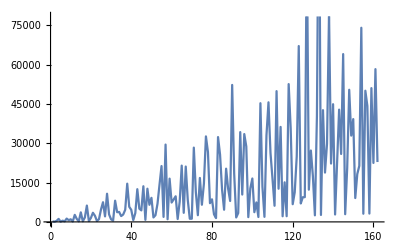

```mathematica
Differences@nprimes[15][[;;163]]//ListLinePlot
```

```mathematica
Position[Differences@nprimes[9][[;;10000]],1085]
```

{{33},{162}}

```mathematica
Select[Differences@nprimes[9][[;;10000]]//Tally,#[[2]]>1&]
```

{{1085,2},{2709,2},{1635,2},{2765,2},{1245,2},{3787,2},{2208,2},{1947,2},{3435,2},{3885,2},{4245,2},{7056,2},{2805,2},{3075,2},{6360,2},{4320,2},{3525,2},{7128,2},{3675,2},{9888,2},{3765,2},{4803,2},{10152,2},{18843,2},{5205,2},{5493,2},{9765,2},{5883,2},{6267,2},{6675,2},{7203,2},{9960,2},{18333,2},{11800,2},{9237,2},{27909,2},{9555,2},{48315,3},{12960,2},{10533,2},{25347,2},{25557,2},{30048,2},{11427,2},{11445,2},{23856,2},{20235,2},{25824,2},{25944,2},{13485,2},{22605,2},{32739,2},{28392,2},{28776,2},{24045,3},{39024,2},{14685,2},{20280,2},{15675,2},{21000,2},{64200,2},{107640,2},{54560,2},{33384,2},{50445,2},{22472,2},{17187,2},{23064,2},{17763,2},{17853,2},{23912,2},{30195,2},{30595,2},{18627,2},{56205,2},{44373,3},{26136,2},{66000,2},{59787,2},{20037,2},{40872,2},{48573,2},{34845,2},{42576,2},{35715,2},{79563,2},{50757,2},{43584,2},{36435,2},{29448,2},{88824,2},{37395,2},{22803,2},{30456,2},{23163,2},{39885,2},{24357,2},{75645,2},{50520,2},{77877,2},{35064,2},{52680,2},{53352,2},{53568,2},{89840,2},{162720,2},{36456,2},{55248,2},{46245,2},{111672,2},{28077,2},{38808,2},{58440,2},{69195,2},{79344,2},{100240,2},{41112,2},{41400,2},{62448,2},{41976,2},{63480,2},{52965,2},{53235,2},{32043,2},{32235,2},{32325,2},{86688,2},{88032,3},{44088,2},{55515,2},{78981,2},{68520,2},{68712,2},{69000,2},{46152,2},{34827,2},{70200,2},{35445,2},{71832,2},{48120,2},{72744,2},{61365,2},{49464,2},{76680,2},{51272,2},{77112,3},{51720,2},{51960,2},{39075,2},{78360,2},{52800,2},{39693,2},{39765,2},{40443,2},{54168,2},{82608,2},{68955,2},{110544,2},{55392,2},{278520,3},{83712,2},{56448,2},{57240,2},{58344,2},{116912,2},{73155,2},{44283,2},{88944,2},{74685,2},{74805,2},{120080,2},{45195,2},{227355,2},{76035,2},{45645,2},{60888,2},{76395,2},{76995,2},{62376,2},{93648,2},{46923,2},{236355,2},{94872,2},{79365,2},{95688,2},{95928,2},{64320,2},{64800,2},{81165,2},{65240,2},{98520,2},{49515,2},{49917,2},{50637,2},{101712,2},{51027,2},{51933,2},{139824,2},{107400,2},{197373,2},{144672,2},{108600,2},{110640,2},{110712,2},{92445,2},{148512,2},{56283,2},{113808,2},{95205,2},{76440,2},{76472,2},{57603,2},{77352,2},{59037,2},{118200,2},{59403,2},{79640,2},{121512,2},{121584,2},{61773,2},{82536,2},{125256,2},{125832,2},{84312,2},{63267,2},{63627,2},{297640,2},{63885,2},{85464,2},{64893,2},{65397,2},{88872,2},{89832,2},{67485,2},{135960,2},{113685,2},{136488,2},{136992,2},{69603,2},{69675,2},{140712,2},{70437,2},{142584,2},{142752,2},{144312,2},{97032,2},{73203,2},{97848,2},{147312,2},{73707,2},{98472,2},{74085,2},{98808,2},{148272,2},{125115,2},{100320,2},{151008,2},{76053,2},{101448,2},{102024,2},{153960,2},{154032,2},{154488,2},{413472,2},{155928,2},{156168,2},{156288,2},{104664,2},{80085,2},{80283,2},{161184,2},{161472,2},{108672,2},{137355,2},{137955,2},{223968,2},{225312,2},{112968,2},{113448,2},{113688,2},{114120,2},{171768,2},{118776,2},{178752,2},{120168,2},{150915,2},{244512,2},{309480,2},{124440,2},{127464,2},{161835,2},{326040,2},{130600,2},{197112,2},{132672,2},{199704,2},{166605,2},{134376,2},{135288,2},{135800,2},{140120,2},{421848,2},{140952,2},{141192,2},{356520,2},{142968,2},{143160,2},{145288,2},{145320,2},{224040,2},{187005,2},{150840,2},{226632,2},{190965,2},{153000,2},{154080,2},{192885,2},{231528,2},{311712,2},{156520,2},{235320,2},{398320,2},{205995,2},{208005,2},{256872,2},{308805,2},{222645,2},{273624,2},{367008,2},{322035,2},{279840,2},{279912,2},{282360,2},{385968,2},{291288,2},{296808,2},{455427,2},{314040,2},{316776,2},{317400,2},{407085,2},{601440,2}}

```mathematica
First/@Select[Differences@nprimes[15][[;;10000]]//Tally,#[[2]]>1&]
```

{12672,52608,56448,557928,573480,7776120}

```mathematica
Table[d->sdl@Differences@nprimes[d][[;;10000]]//N,{d,2,16}]//TableForm
```

2.→<|sdl→0.82877,h→0.7069|>
3.→<|sdl→0.011687,h→0.99707|>
4.→<|sdl→0.906077,h→0.653235|>
5.→<|sdl→0.,h→1.|>
6.→<|sdl→0.648166,h→0.796578|>
7.→<|sdl→0.,h→1.|>
8.→<|sdl→0.84645,h→0.695927|>
9.→<|sdl→0.00571978,h→0.998568|>
10.→<|sdl→0.839928,h→0.700045|>
11.→<|sdl→0.,h→1.|>
12.→<|sdl→0.71922,h→0.764944|>
13.→<|sdl→0.,h→1.|>
14.→<|sdl→0.976228,h→0.577091|>
15.→<|sdl→0.000100596,h→0.999975|>
16.→<|sdl→0.717343,h→0.765828|>